# Visualization Try-out Notebook

## from Jialin Lu mailbox at: luxxxlucy@gmail.com

## 2D Visualizations

Making a Stream Plot of Vectors

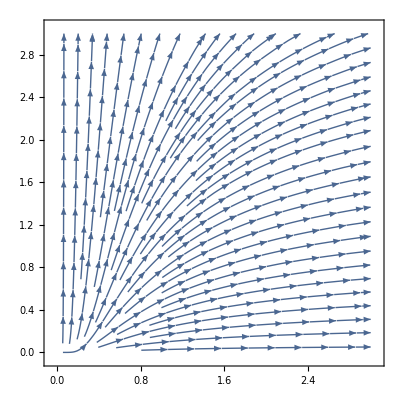

```mathematica
StreamPlot[{x^2,y},{x,0,3},{y,0,3} ]
```

Plot a region of given constraints

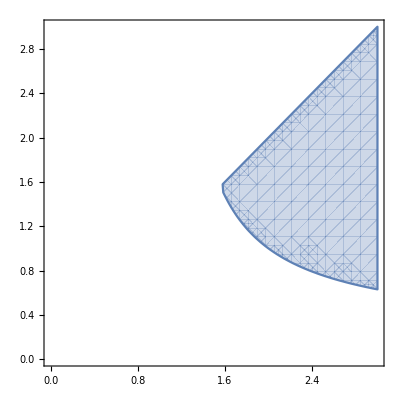

```mathematica
RegionPlot [x^y>2 && y<x,{x,0,3},{y,0,3} ]
```

Animations that changes given time

```mathematica
Animate[Plot[Sin[t-x],{x,0,10}],{t,0,10}]
```

Automaton

```mathematica
(* Rule 110 *)
ArrayPlot@CellularAutomaton[110,{{1},0},100]
(* The Conway's game of life *) 
Manipulate[Module[{matrix},SeedRandom[seed]; matrix=RandomInteger[{1},{cells,cells}]; f[#,ImageSize->{375,375}]&@@ CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}}, matrix,{{step}}]], {step,0,1000,1,Appearance->"Labeled",ControlPlacement->Left,ImageSize->Tiny}, {{seed,1,"initial condition"},1,2000,1,ControlPlacement->Left,ImageSize->Tiny}, {{cells,20,"number of vertices"},10,50,1,Appearance->"Labeled",ControlPlacement->Left,ImageSize->Tiny},{{f,ArrayPlot,"type of plot"},{ArrayPlot,GraphPlot,GraphPlot3D,LayeredGraphPlot,TreePlot}},AutorunSequencing->{3,4}]
```

-Graphics-

Simple Manipulation

```mathematica
Manipulate[Plot[x^2a+x*b,{x,-3,3}],{a,.1,3},{b,0,3}]
```

Make Mosaic

```mathematica
imagePool=Map[With[{i=Import[#]},{i,Mean[Flatten[N[i[[1,1]]],1]]}]&,FileNames["Pool/*.jpg"]];
closeMatch[c_]:=RandomChoice[Take[SortBy[imagePool,Norm[c-#[[2]]]&],20]][[1]];
Grid[Reverse[Map[closeMatch,Import["MasterImage.tif"][[1,1]],{2}]],Spacings->{0,0}]

(*作者：加刘景长
链接：https://www.zhihu.com/question/27834147/answer/38388593
来源：知乎
著作权归作者所有。商业转载请联系作者获得授权，非商业转载请注明出处。*)
```